```mathematica
ClearAll["Global`*"]
```

# Input Mesh

Here we set input mesh for our project. Then cpp unit ../../user.cpp loads mesh data structure, (uniformly) refines it several times, and saves coarse and fine meshes + their ribs’ numeration—we will need this since ribs’ numeration is DOFs numeration for Crouzeix–Raviart shape funcs—to ../Projection and Restriction Visualization/meshes.

## Set Analytic Region Ω

```mathematica
(*Ω=MeshRegion[{
{1,0},{2,0},
{0,1},{1,1},{2,1},
{0,2},{1,2},{2,2}
},
Triangle@{
{1,2,4},{2,5,4},
{4,5,7},{5,8,7},
{3,4,6},{4,7,6}
}
];*)
Ω=Rectangle[];
```

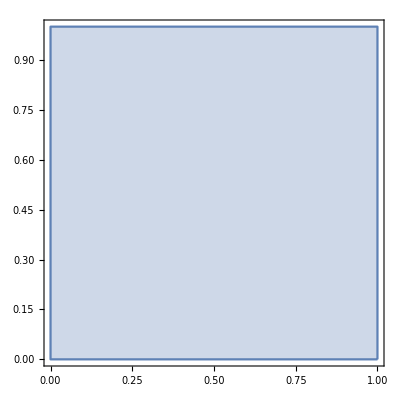

```mathematica
RegionPlot@Ω
```

## Create and Export Resulting Mesh 𝒯

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
𝒯=create𝒯fromRegion[Ω,.1];
```

```mathematica
highlight[𝒯,{"localNodesNumn","nodesNumn","trianglesNumn"}]
```

-Graphics-

### Export

```mathematica
(* set your home directory *)
SetDirectory@NotebookDirectory[];
export@𝒯
```

mesh.ntn